Helper tools

```mathematica
ClearAll["Global`*"]
basepath="/Users/basavyr/Documents/Work/Repos/mathematica-useful-algorithms/Physics/Elliptic-Functions-New-Boson/Figures/Frequencies";
export[object_,name_,format_]:=Export[StringTemplate["``/``.``"][basepath,name,format],object, ImageResolution->1500];
linspace[a_,b_,n_]:=Table[N[q],{q,a,b,(b-a)/(n-1)}];
```

Numerical values

```mathematica
MOIfit1={91,9,51};
MOIfit2={13.53,101.76,52.94};
MOIfit3={89,12,48};
thetadegfit1=-119;
thetadegfit2=140;
thetadegfit3=-71;
oddspin=5.5;
Ak[mois_]:=N[1/(2*#)]&/@mois;
rad[thetadeg_]:=N[thetadeg*π/180];
j1[thetadeg_]:=oddspin*Cos[rad[thetadeg]];
j2[thetadeg_]:=oddspin*Sin[rad[thetadeg]];
```

Analytical Formulas

```mathematica
A[I_,thetadeg_,mois_]:=Ak[mois][[2]](1-j2[thetadeg]/I)-Ak[mois][[1]];
u[I_,thetadeg_,mois_]:=(Ak[mois][[3]]-Ak[mois][[1]])/A[I,thetadeg,mois];
v0[I_,thetadeg_,mois_]:=-(Ak[mois][[1]]*j1[thetadeg])/A[I,thetadeg,mois];
```

## The wobbling frequency evaluated for 135Pr

Omega ω

```mathematica
A21[I_,thetadeg_,mois_]:=(Ak[mois][[2]]-Ak[mois][[1]]-(Ak[mois][[2]]*j2[thetadeg])/I);
omega[I_,thetadeg_,mois_]:=(((2I+1)*A21[I,thetadeg,mois]+2*Ak[mois][[1]]*j1[thetadeg])*((2I+1)*(Ak[mois][[3]]-Ak[mois][[1]])+2*Ak[mois][[1]]*j1[thetadeg])-(Ak[mois][[3]]-Ak[mois][[1]])*A21[I,thetadeg,mois])^(1/2);
```

Graphical representations for ω

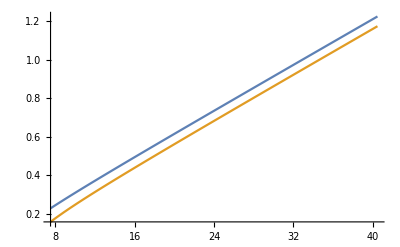

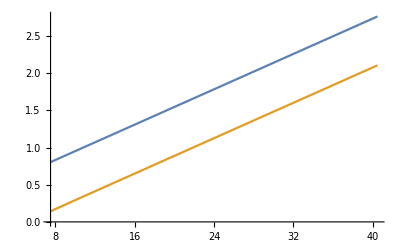

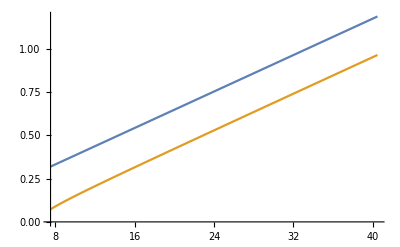

```mathematica
Plot[{omega[x,thetadegfit1,MOIfit1],omega[x,thetadegfit1+180,MOIfit1]},{x,7.5,40.5}]
Plot[{omega[x,thetadegfit2,MOIfit2],omega[x,thetadegfit2+180,MOIfit2]},{x,7.5,40.5}]
Plot[{omega[x,thetadegfit3,MOIfit3],omega[x,thetadegfit3+180,MOIfit3]},{x,7.5,40.5}]
```